# (31 Jan 1 Feb 2 Feb) 2017 NW GaAs AB225 AB232 AlGaAs

```mathematica
ClearAll[jan31]
jan31=Table[Import["C:\\Users\\tonie\\Desktop\\учеба\\НИР\\Data\\2017\\jan\\31\\31jan_acuun_"<>ToString[i]<>".dat"],{i,1,8}];
ClearAll[feb1]
feb1=Table[Import["C:\\Users\\tonie\\Desktop\\учеба\\НИР\\Data\\2017\\feb\\1\\1feb_acuun_"<>ToString[i]<>".dat"],{i,1,13}];
ClearAll[feb2]
feb2=Table[Import["C:\\Users\\tonie\\Desktop\\учеба\\НИР\\Data\\2017\\feb\\2\\2feb_acuun_"<>ToString[i]<>".dat"],{i,1,13}];
```

```mathematica
TableForm[Import["C:\\Users\\tonie\\Desktop\\учеба\\НИР\\Data\\2017\\jan\\31\\31jan_tds_2.dat"][[1;;10]]]
```

-101.5 | 0.00077225 | -5.75×10^-6 | 0. | 101.5
-101.55 | 0.00077775 | -0.000027 | 0.333567 | 101.55
-101.6 | 0.0007875 | -0.00002525 | 0.667133 | 101.6
-101.65 | 0.0007865 | -0.00001975 | 1.0007 | 101.65
-101.7 | 0.00075775 | -5.25×10^-6 | 1.33427 | 101.7
-101.75 | 0.000777 | -0.00003725 | 1.66783 | 101.75
-101.8 | 0.0007555 | 3.25×10^-6 | 2.0014 | 101.8
-101.85 | 0.000769 | -0.0000305 | 2.33497 | 101.85
-101.9 | 0.0007995 | -0.00001775 | 2.66853 | 101.9
-101.95 | 0.00080175 | -0.00004725 | 3.0021 | 101.95

```mathematica
feb1[[6]][[1,2]]
```

0.000319231

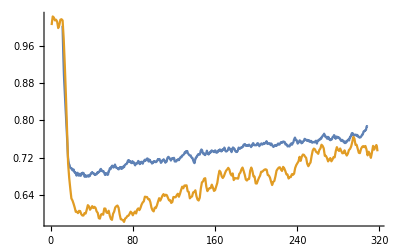

```mathematica
ListLinePlot[
{
MeanFilter[Import["C:\\Users\\tonie\\Desktop\\учеба\\НИР\\Data\\2017\\jan\\31\\31jan_tds_2.dat"][[All,{4,2}]]/.{x_,y_}->{x+10,y/Import["C:\\Users\\tonie\\Desktop\\учеба\\НИР\\Data\\2017\\jan\\31\\31jan_tds_2.dat"][[1,2]]},{10,0}],
MeanFilter[feb1[[6]][[All,{3,2}]]/.{x_,y_}->{x,y/feb1[[6]][[1,2]]},{2,0}]
},
PlotRange->All
]
```

```mathematica
ClearAll[shortAB225,longFeb1,shortFeb1,shortFeb2AB225,shortFeb2AB332, allDat31]
shortAB225 = {"shortAB225",jan31[[{2,3,6,4,5}]]};
longFeb1 = {"longFeb1AB225",feb1[[{11,9,6}]]};
longFeb1[[2,3,All,3]] = longFeb1[[2,3,All,3]]-11.2;
shortFeb1 = {"shortFeb1AB225",feb1[[{10,8,7}]]};
shortFeb2AB332 = {"shortFeb2AB332",feb2[[{5,4,3}]]};
shortFeb2AB225 = {"shortFeb2AB225",feb2[[{11,10,9,8}]]};
allDat31 = {shortAB225,longFeb1,shortFeb1,shortFeb2AB225,shortFeb2AB332};
```

```mathematica
ClearAll[powerDatDict31]
powerDatDict31 = 
<|
"shortAB225"->{"2 ?","3 ?",0.5,4,1},
"longFeb1AB225"->{1,2,4},
"shortFeb1AB225"->{1,2,4},
"shortFeb2AB332"->{2,4,3},
"shortFeb2AB225"->{1,2,3,4}
|>;
```

```mathematica
TableForm[Table[Table[allDat31[[j]][[2,i]][[1,1]],{i,Length[allDat31[[j,2]]]}],{j,Length[allDat31]}]]
```

-101.5 | -101.5 | -101.5 | -101.5 | -101.5
-101.5 | -101.5 | -100. |  | 
-101.5 | -101.5 | -101.5 |  | 
-101.75 | -101.75 | -101.75 | -101.75 | 
-101.95 | -101.95 | -101.95 |  |

#### All measures

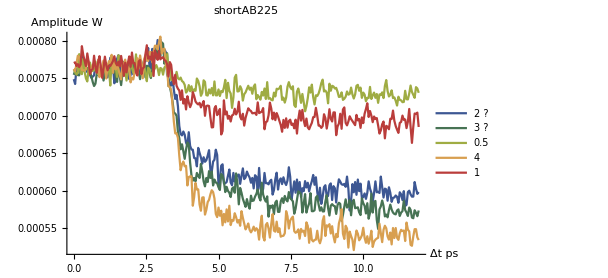
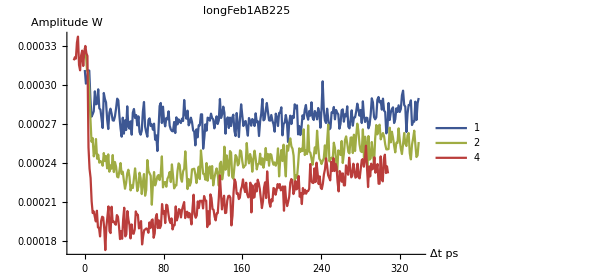
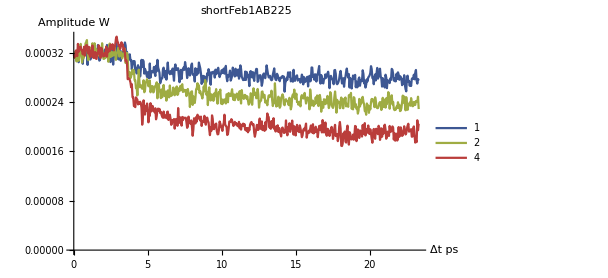
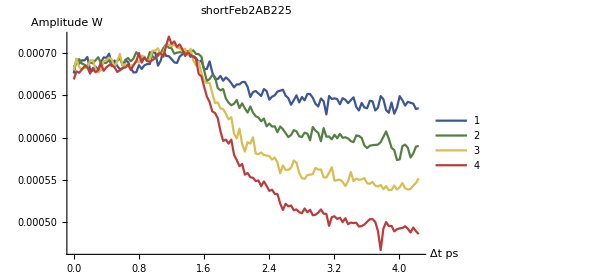
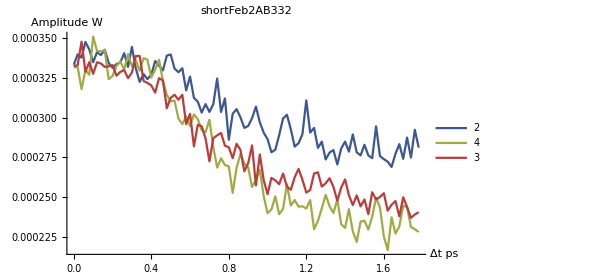

```mathematica
Row[
Table[
ListLinePlot[
Table[dat[[2,i]][[All,{3,2}]],{i,1,Length[dat[[2]]]}],
ImageSize->450,
AxesLabel->{"Δt ps","Amplitude W"},
PlotLabel->dat[[1]],
LabelStyle->15,
PlotStyle->"DarkRainbow",
PlotRange->All,
PlotLegends->powerDatDict31[dat[[1]]]],
{dat,allDat31}]
]
```

```mathematica
amplitudes=
Table[
{
dat[[1]],
Table[
MeanFilter[
(dat[[2]][[i,All,2]]+(Max[dat[[2]][[All,1,2]]]-dat[[2]][[i,1,2]]))/Max[dat[[2]][[All,1,2]]],
1],
{i,1,Length[dat[[2]]]}]
},
{dat,allDat31}];
```

```mathematica
normDatDic = 
Association[
Table[
amplitudes[[i,1]]->
Table[
Transpose[{allDat31[[i,2]][[j,All,3]],amplitudes[[i,2]][[j]]}],
{j,Length[allDat31[[i,2]]]}],
{i,Length[amplitudes]}
]
];
```

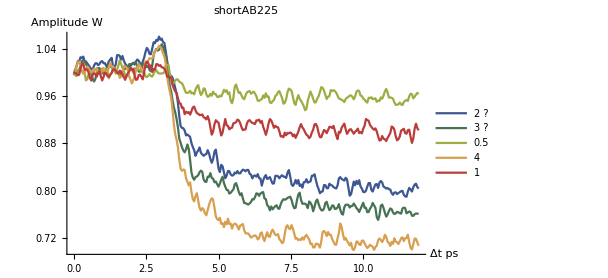
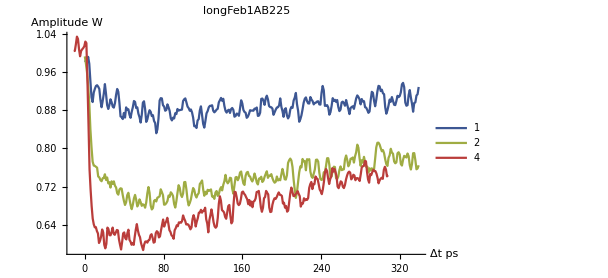
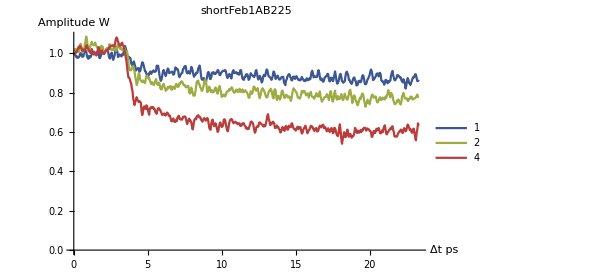
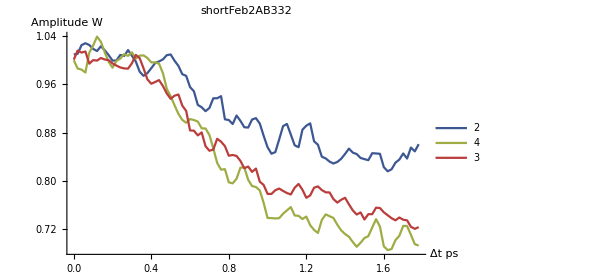
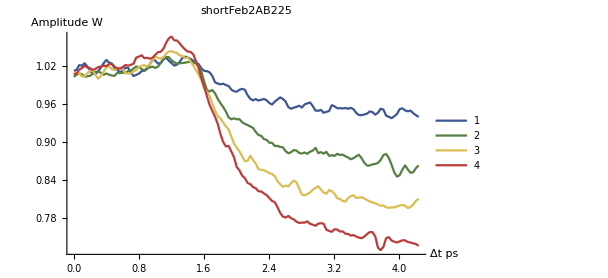

```mathematica
Row[
Table[
ListLinePlot[
normDatDic[name],
ImageSize->450,
AxesLabel->{"Δt ps","Amplitude W"},
PlotLabel->name,
LabelStyle->15,
PlotStyle->"DarkRainbow",
PlotRange->All,
PlotLegends->powerDatDict31[name]],
{name,Keys[powerDatDict31]}]
]
```

#### Logarithmic scaling

```mathematica
normLogDatDic = 
Association[
Table[
amplitudes[[i,1]]->
Table[
Transpose[{allDat31[[i,2]][[j,All,3]],Log[amplitudes[[i,2]][[j]]]}],
{j,Length[allDat31[[i,2]]]}],
{i,Length[amplitudes]}
]
];
```

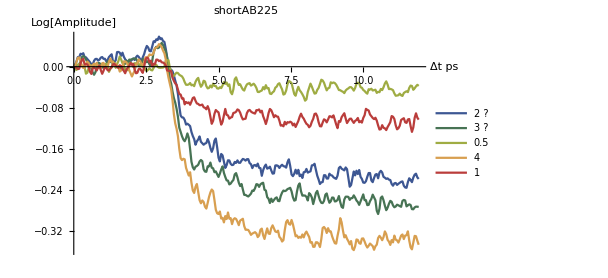
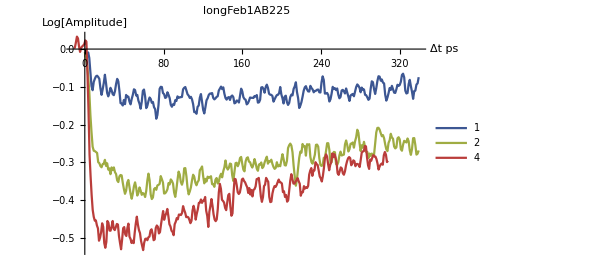
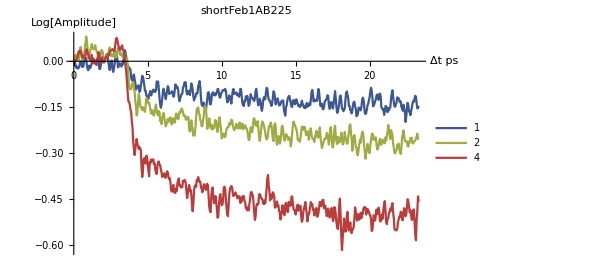
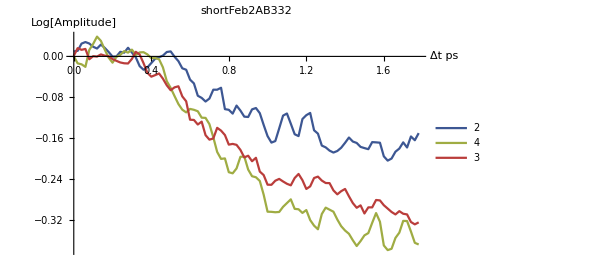
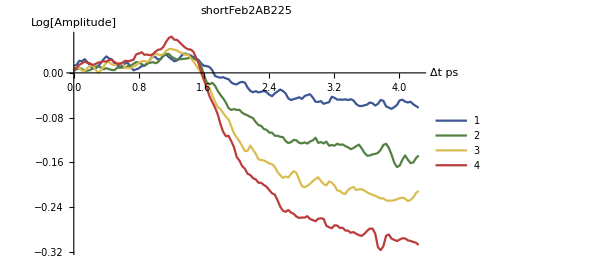

```mathematica
Row[
Table[
ListLinePlot[
normLogDatDic[name],
ImageSize->450,
AxesLabel->{"Δt ps","Log[Amplitude]"},
PlotLabel->name,
LabelStyle->15,
PlotStyle->"DarkRainbow",
PlotRange->All,
PlotLegends->powerDatDict31[name]],
{name,Keys[powerDatDict31]}]
]
```

Short dynamic

#### Short dynamic for shortAB225

```mathematica
Keys[powerDatDict31]
```

{shortAB225,longFeb1AB225,shortFeb1AB225,shortFeb2AB332,shortFeb2AB225}

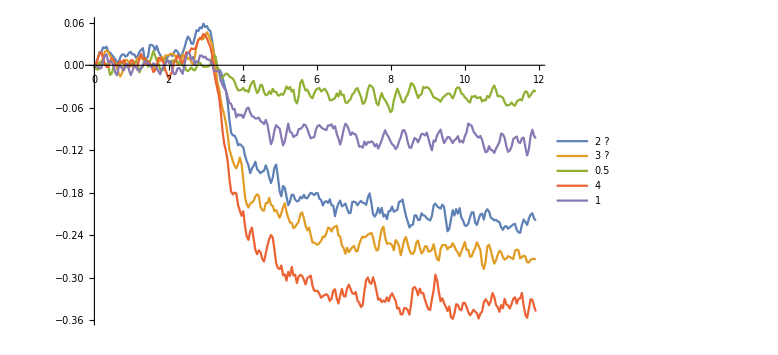

```mathematica
ListLinePlot[normLogDatDic["shortAB225"],PlotLegends->powerDatDict31["shortAB225"],ImageSize->Large]
```

Linear area for this sample

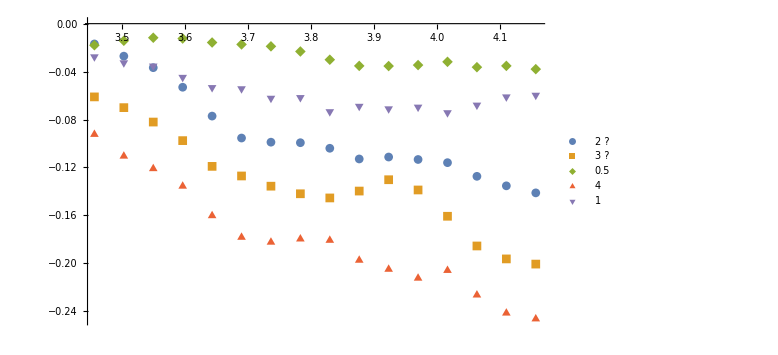

```mathematica
ListPlot[normLogDatDic["shortAB225"][[All,75;;90]],PlotLegends->powerDatDict31["shortAB225"],ImageSize->Large,PlotMarkers->Automatic]
```

```mathematica
lineEreaShortAB225 = normLogDatDic["shortAB225"][[;;,75;;90]];
```

```mathematica
lineCoefShortAB225 = Table[FindFit[lineEreaShortAB225[[i]],a t+b,{a,b},t],{i,1,Length[lineEreaShortAB225]}];
```

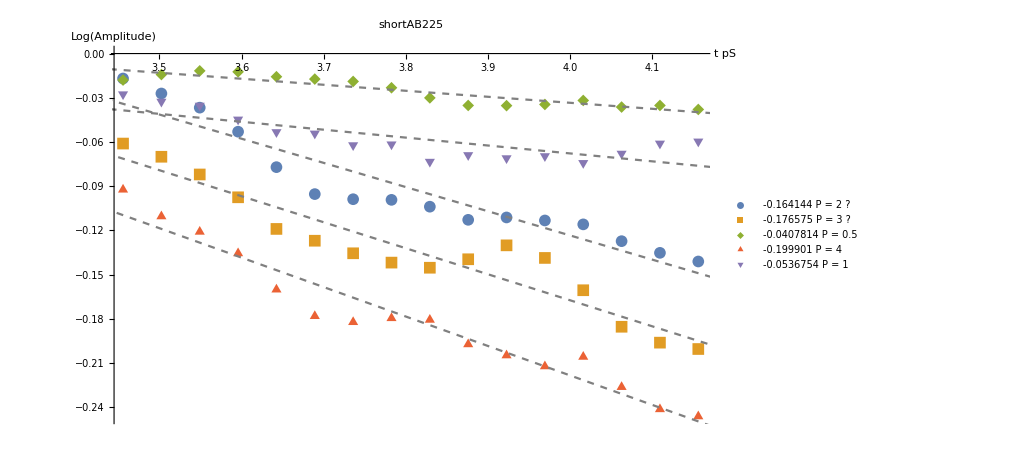

```mathematica
Show[
ListPlot[
Table[lineEreaShortAB225[[i]],{i,1,5}],
PlotLegends->Table[ToString[lineCoefShortAB225[[i,1,2]]]<>"    P = "<>ToString[powerDatDict31["shortAB225"][[i]]],{i,1,5}],
ImageSize->750,
PlotLabel->"shortAB225",
AxesLabel->{"t pS","Log(Amplitude)"},
LabelStyle->18,
PlotMarkers->{Automatic,12}
],
Plot[
Table[a x+b/.lineCoefShortAB225[[i]],{i,1,5}],
{x,3.2,4.3},
PlotStyle->{Gray,Dashed}
]
]
```

#### Short dynamic for shortFeb1AB225

```mathematica
Keys[powerDatDict31]
```

{shortAB225,longFeb1AB225,shortFeb1AB225,shortFeb2AB332,shortFeb2AB225}

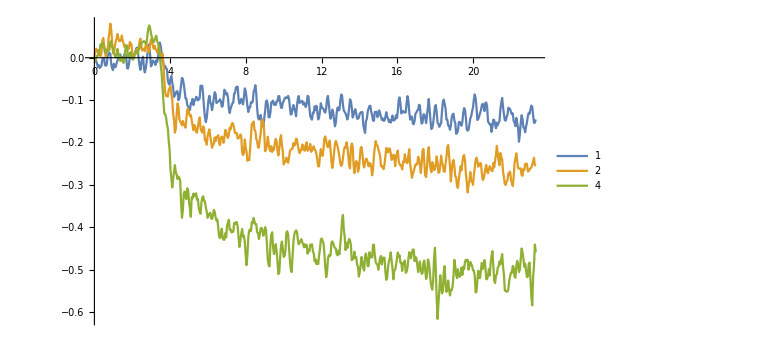

```mathematica
ListLinePlot[normLogDatDic["shortFeb1AB225"],PlotLegends->powerDatDict31["shortFeb1AB225"],ImageSize->Large]
```

Linear area for this sample

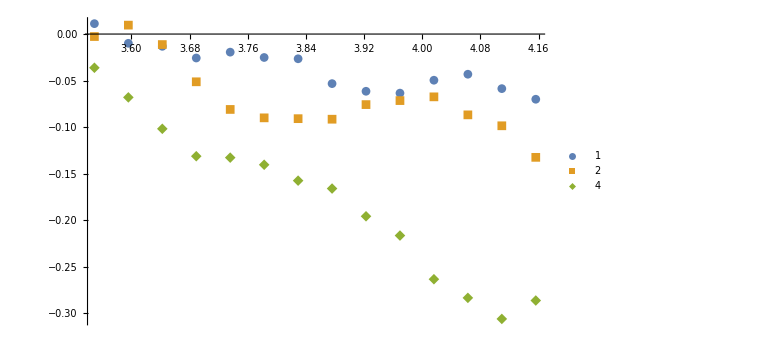

```mathematica
ListPlot[normLogDatDic["shortFeb1AB225"][[All,77;;90]],PlotLegends->powerDatDict31["shortFeb1AB225"],ImageSize->Large,PlotMarkers->Automatic]
```

```mathematica
lineEreaShortFeb1AB225 = normLogDatDic["shortFeb1AB225"][[All,77;;90]];
```

```mathematica
lineCoefShortFeb1AB225 = Table[FindFit[lineEreaShortFeb1AB225[[i]],a t+b,{a,b},t],{i,1,Length[lineEreaShortFeb1AB225]}];
```

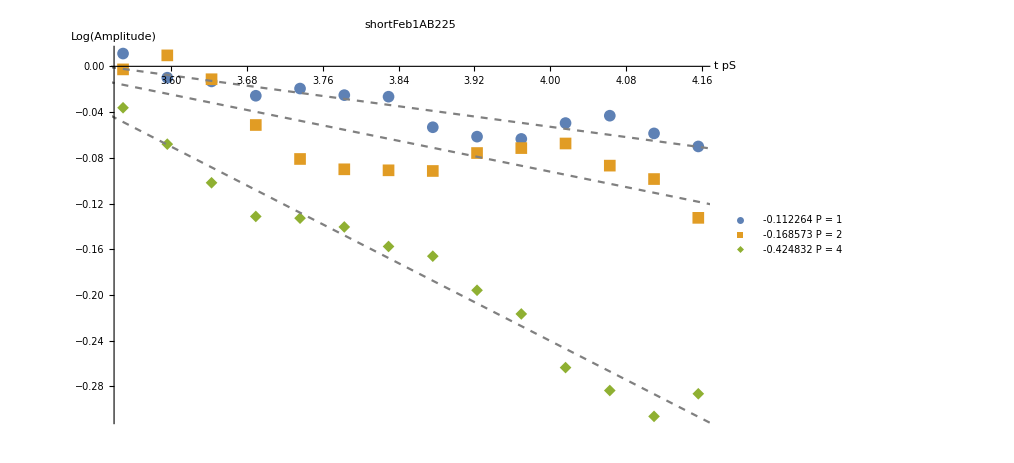

```mathematica
Show[
ListPlot[
Table[lineEreaShortFeb1AB225[[i]],{i,1,3}],
PlotLegends->Table[ToString[lineCoefShortFeb1AB225[[i,1,2]]]<>"    P = "<>ToString[powerDatDict31["shortFeb1AB225"][[i]]],{i,1,3}],
ImageSize->750,
PlotLabel->"shortFeb1AB225",
AxesLabel->{"t pS","Log(Amplitude)"},
LabelStyle->18,
PlotMarkers->{Automatic,12}
],
Plot[
Table[a x+b/.lineCoefShortFeb1AB225[[i]],{i,1,3}],
{x,3.2,4.3},
PlotStyle->{Gray,Dashed}
]
]
```

#### Short dynamic for shortFeb2AB332

```mathematica
Keys[powerDatDict31]
```

{shortAB225,longFeb1AB225,shortFeb1AB225,shortFeb2AB332,shortFeb2AB225}

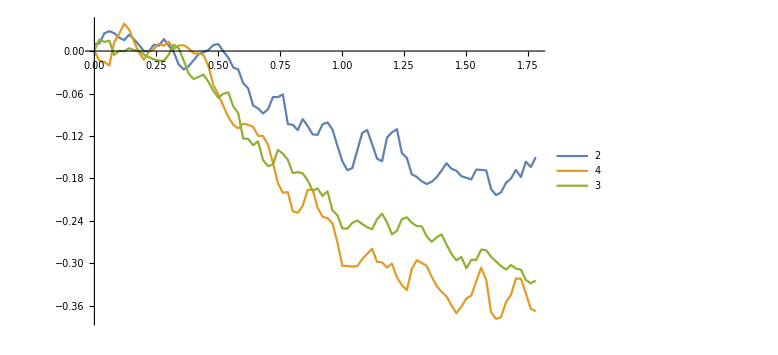

```mathematica
ListLinePlot[normLogDatDic["shortFeb2AB332"],PlotLegends->powerDatDict31["shortFeb2AB332"],ImageSize->Large]
```

Linear area for this sample

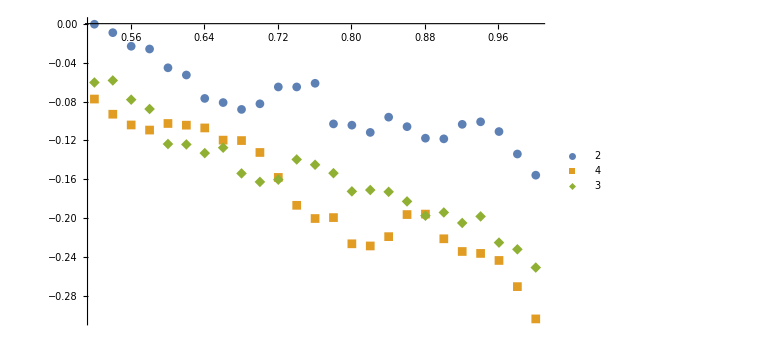

```mathematica
ListPlot[normLogDatDic["shortFeb2AB332"][[All,27;;51]],PlotLegends->powerDatDict31["shortFeb2AB332"],ImageSize->Large,PlotMarkers->Automatic]
```

```mathematica
lineEreaShortFeb2AB332 = normLogDatDic["shortFeb2AB332"][[All,27;;51]];
```

```mathematica
lineCoefShortFeb2AB332 = Table[FindFit[lineEreaShortFeb2AB332[[i]],a t+b,{a,b},t],{i,1,Length[lineEreaShortFeb2AB332]}];
```

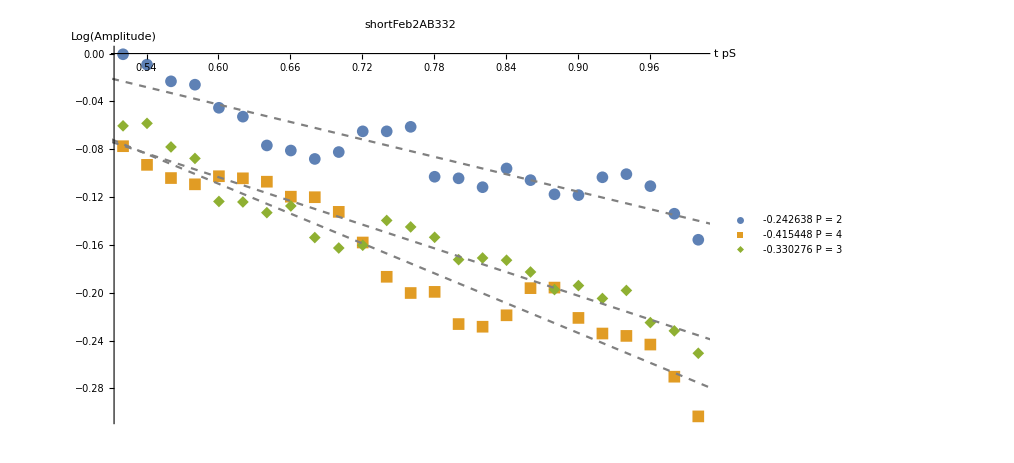

```mathematica
Show[
ListPlot[
Table[lineEreaShortFeb2AB332[[i]],{i,1,3}],
PlotLegends->Table[ToString[lineCoefShortFeb2AB332[[i,1,2]]]<>"    P = "<>ToString[powerDatDict31["shortFeb2AB332"][[i]]],{i,1,3}],
ImageSize->750,
PlotLabel->"shortFeb2AB332",
AxesLabel->{"t pS","Log(Amplitude)"},
LabelStyle->18,
PlotMarkers->{Automatic,12}
],
Plot[
Table[a x+b/.lineCoefShortFeb2AB332[[i]],{i,1,3}],
{x,.5,1.2},
PlotStyle->{Gray,Dashed}
]
]
```

#### Short dynamic for shortFeb2AB225

```mathematica
Keys[powerDatDict31]
```

{shortAB225,longFeb1AB225,shortFeb1AB225,shortFeb2AB332,shortFeb2AB225}

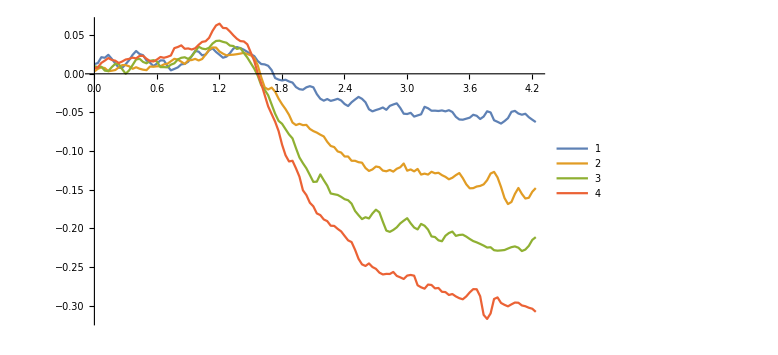

```mathematica
ListLinePlot[normLogDatDic["shortFeb2AB225"],PlotLegends->powerDatDict31["shortFeb2AB225"],ImageSize->Large]
```

Linear area for this sample

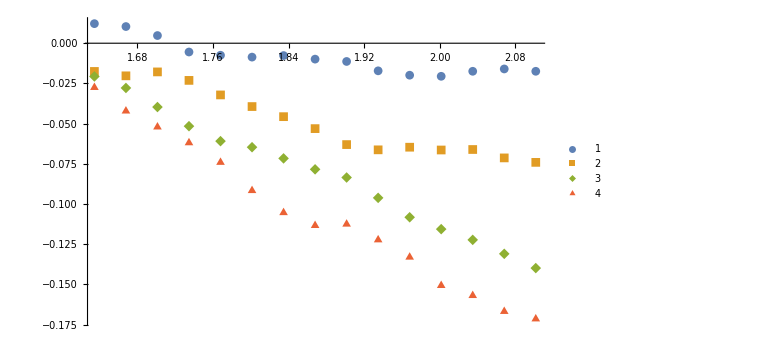

```mathematica
ListPlot[normLogDatDic["shortFeb2AB225"][[All,50;;64]],PlotLegends->powerDatDict31["shortFeb2AB225"],ImageSize->Large,PlotMarkers->Automatic]
```

```mathematica
lineEreaShortFeb2AB225 = normLogDatDic["shortFeb2AB225"][[All,50;;64]];
```

```mathematica
lineCoefShortFeb2AB225 = Table[FindFit[lineEreaShortFeb2AB225[[i]],a t+b,{a,b},t],{i,1,Length[lineEreaShortFeb2AB225]}];
```

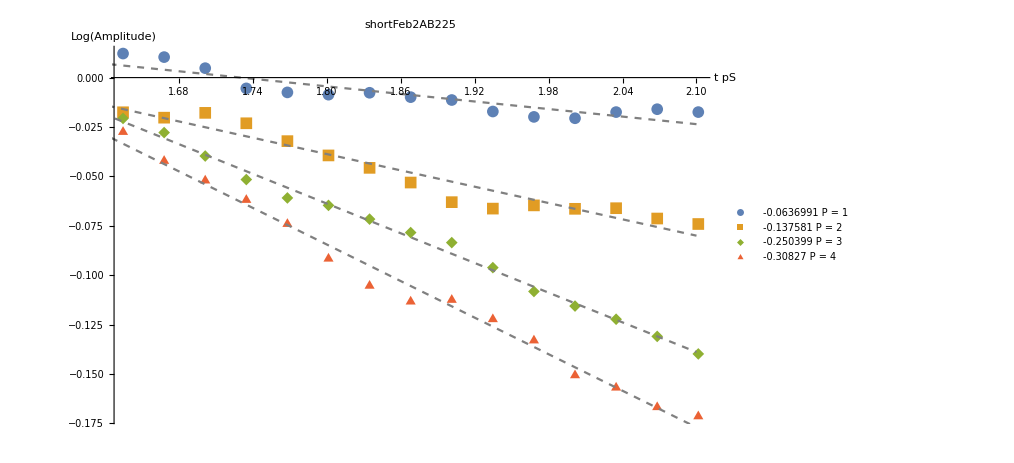

```mathematica
Show[
ListPlot[
Table[lineEreaShortFeb2AB225[[i]],{i,1,4}],
PlotLegends->Table[ToString[lineCoefShortFeb2AB225[[i,1,2]]]<>"    P = "<>ToString[powerDatDict31["shortFeb2AB225"][[i]]],{i,1,4}],
ImageSize->750,
PlotLabel->"shortFeb2AB225",
AxesLabel->{"t pS","Log(Amplitude)"},
LabelStyle->18,
PlotMarkers->{Automatic,12}
],
Plot[
Table[a x+b/.lineCoefShortFeb2AB225[[i]],{i,1,4}],
{x,1.5,2.1},
PlotStyle->{Gray,Dashed}
]
]
```

#### Short dynamic comparison

```mathematica
Keys[powerDatDict31]
```

{shortAB225,longFeb1AB225,shortFeb1AB225,shortFeb2AB332,shortFeb2AB225}

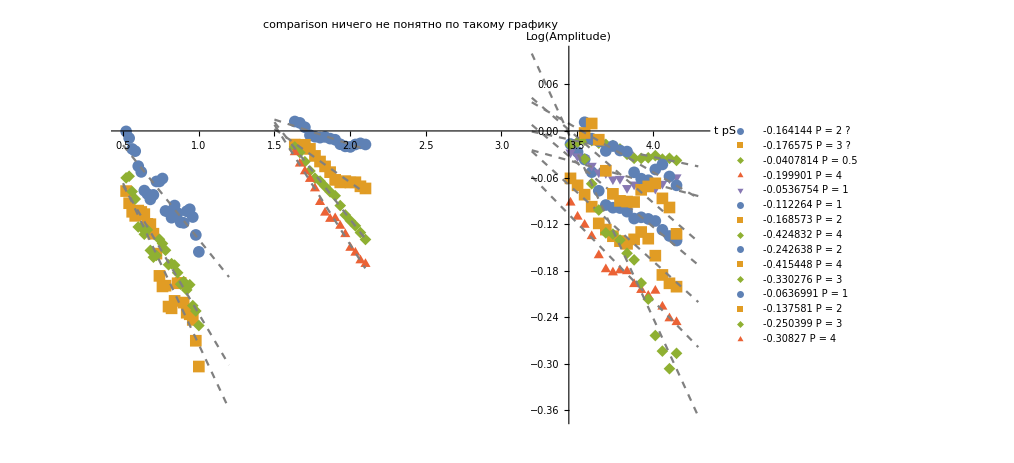

```mathematica
Show[
ListPlot[
Table[lineEreaShortAB225[[i]],{i,1,5}],
PlotLegends->Table[ToString[lineCoefShortAB225[[i,1,2]]]<>"    P = "<>ToString[powerDatDict31["shortAB225"][[i]]],{i,1,5}],
ImageSize->750,
PlotLabel->"shortAB225",
AxesLabel->{"t pS","Log(Amplitude)"},
LabelStyle->18,
PlotMarkers->{Automatic,12}
],
Plot[
Table[a x+b/.lineCoefShortAB225[[i]],{i,1,5}],
{x,3.2,4.3},
PlotStyle->{Gray,Dashed}
],
ListPlot[
Table[lineEreaShortFeb1AB225[[i]],{i,1,3}],
PlotLegends->Table[ToString[lineCoefShortFeb1AB225[[i,1,2]]]<>"    P = "<>ToString[powerDatDict31["shortFeb1AB225"][[i]]],{i,1,3}],
ImageSize->750,
PlotLabel->"shortFeb1AB225",
AxesLabel->{"t pS","Log(Amplitude)"},
LabelStyle->18,
PlotMarkers->{Automatic,12}
],
Plot[
Table[a x+b/.lineCoefShortFeb1AB225[[i]],{i,1,3}],
{x,3.2,4.3},
PlotStyle->{Gray,Dashed}
],
ListPlot[
Table[lineEreaShortFeb2AB332[[i]],{i,1,3}],
PlotLegends->Table[ToString[lineCoefShortFeb2AB332[[i,1,2]]]<>"    P = "<>ToString[powerDatDict31["shortFeb2AB332"][[i]]],{i,1,3}],
ImageSize->750,
PlotLabel->"shortFeb2AB332",
AxesLabel->{"t pS","Log(Amplitude)"},
LabelStyle->18,
PlotMarkers->{Automatic,12}
],
Plot[
Table[a x+b/.lineCoefShortFeb2AB332[[i]],{i,1,3}],
{x,.5,1.2},
PlotStyle->{Gray,Dashed}
],
ListPlot[
Table[lineEreaShortFeb2AB225[[i]],{i,1,4}],
PlotLegends->Table[ToString[lineCoefShortFeb2AB225[[i,1,2]]]<>"    P = "<>ToString[powerDatDict31["shortFeb2AB225"][[i]]],{i,1,4}],
ImageSize->750,
PlotLabel->"shortFeb2AB225",
AxesLabel->{"t pS","Log(Amplitude)"},
LabelStyle->18,
PlotMarkers->{Automatic,12}
],
Plot[
Table[a x+b/.lineCoefShortFeb2AB225[[i]],{i,1,4}],
{x,1.5,2.1},
PlotStyle->{Gray,Dashed}
],
PlotRange->All,
AxesLabel->{"t pS","Log(Amplitude)"},
ImageSize->750,
PlotLabel->"comparison ничего не понятно по такому графику",
LabelStyle->{Black,16}
]
```

```mathematica
Keys[powerDatDict31]
```

{shortAB225,longFeb1AB225,shortFeb1AB225,shortFeb2AB332,shortFeb2AB225}

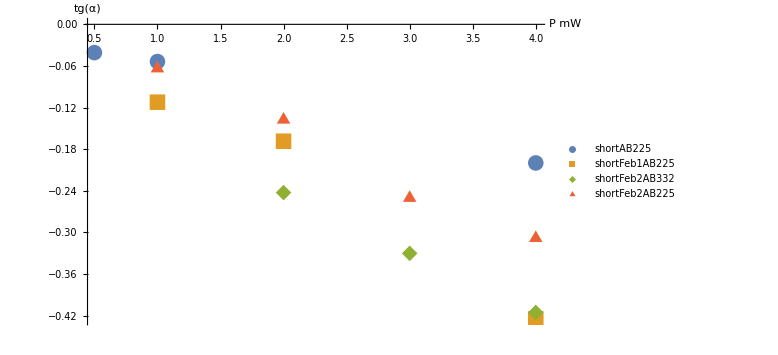

```mathematica
ListPlot[{
Sort[Table[{powerDatDict31["shortAB225"][[i]],lineCoefShortAB225[[i,1,2]]},{i,1,5}]],Sort[Table[{powerDatDict31["shortFeb1AB225"][[i]],lineCoefShortFeb1AB225[[i,1,2]]},{i,1,3}]],
Sort[Table[{powerDatDict31["shortFeb2AB332"][[i]],lineCoefShortFeb2AB332[[i,1,2]]},{i,1,3}]],
Sort[Table[{powerDatDict31["shortFeb2AB225"][[i]],lineCoefShortFeb2AB225[[i,1,2]]},{i,1,4}]]
},
PlotRange->All,
PlotLegends->{"shortAB225","shortFeb1AB225","shortFeb2AB332","shortFeb2AB225"},
LabelStyle->{Black,16},
ImageSize->Large,
AxesLabel->{"P mW","tg(α)"},
PlotMarkers->{Automatic,16}
]
```

```mathematica
Keys[powerDatDict31]
```

{shortAB225,longFeb1AB225,shortFeb1AB225,shortFeb2AB332,shortFeb2AB225}

Long dynamic

```mathematica
Dimensions[normDatDic["longFeb1AB225"]]
```

{3,300,2}

#### Long dynamic for AB225

```mathematica
Manipulate[
Row[
Table[
Show[{
ListLinePlot[
normDatDic["longFeb1AB225"][[i]]
],
Graphics[Line[{{normDatDic["longFeb1AB225"][[i,<|1->a,2->b,3->c|>[i],1]],0},{normDatDic["longFeb1AB225"][[i,<|1->a,2->b,3-> c|>[i],1]],1}}]]
},
PlotRange->{{0,300},{0.5,1}},
AxesOrigin->{0,0},
LabelStyle->{Black,12},
ImageSize->370,
AxesLabel->{"t pS","Amplitude"},
PlotLabel->"Long dynamic for AB225 with P_pump="<>ToString[powerDatDict31["longFeb1AB225"][[i]]]<>" mW"],
{i,{1,2,3}}
]
],
{a,63,100,1},{b,64,100,1},{c,55,100,1}]
```

```mathematica
initials = <|1->63,2->68,3->68|>;
```

```mathematica
expr = Hold@((1-normDatDic["longFeb1AB225"][[i,initials[i],2]])*(1-a Exp[-(t-normDatDic["longFeb1AB225"][[i,initials[i],1]])/c]-(1-a) Exp[-(t-normDatDic["longFeb1AB225"][[i,initials[i],1]])/d])+normDatDic["longFeb1AB225"][[i,initials[i],2]]);
```

```mathematica
coef = 
Association[
Table[
{i->
FindFit[
normDatDic["longFeb1AB225"][[i,initials[i];;]],
{ReleaseHold@expr},
{a,c,d},t]
},
{i,{1,2,3}}
]
];
```

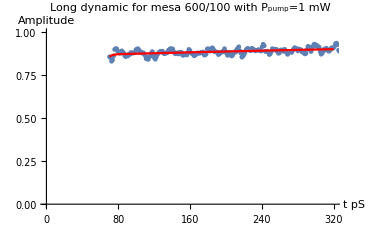
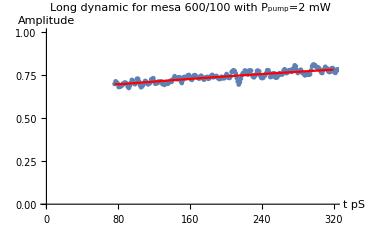
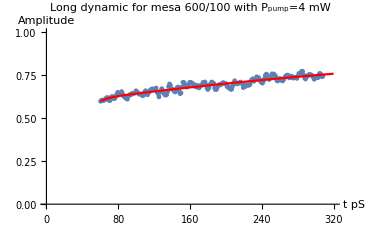

```mathematica
Row[
Table[
Show[
{
ListPlot[
normDatDic["longFeb1AB225"][[i,initials[i];;]]
],
Plot[
(ReleaseHold@expr)/.coef[i],
{t,normDatDic["longFeb1AB225"][[i,initials[i],1]],320},
PlotStyle->Red
]
},
PlotRange->{{0,320},{0,1}},
AxesOrigin->{0,0},
LabelStyle->{Black,12},
ImageSize->370,
AxesLabel->{"t pS","Amplitude"},
PlotLabel->"Long dynamic for mesa 600/100 with P_pump="<>ToString[powerDatDict31["longFeb1AB225"][[i]]]<>" mW"
],
{i,{1,2,3}}
]
]
```

```mathematica
TableForm[Table[{"P = "<>ToString[powerDatDict31["longFeb1AB225"][[k]]],coef[k]},{k,Keys[coef]}]]
```

P = 1 | a→0.901441
c→925.129
d→2.86125
P = 2 | a→1.01541
c→720.479
d→2.3031
P = 4 | a→0.953862
c→561.845
d→8.66265

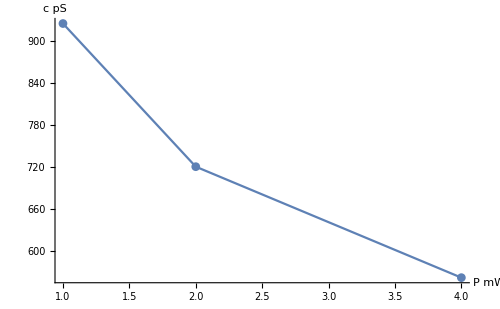

```mathematica
ListLinePlot[
{Sort[Table[{powerDatDict31["longFeb1AB225"][[k]],coef[k][[2,2]]},{k,Keys[coef]}]]},
PlotMarkers->Automatic,
ImageSize->500,
AxesLabel->{"P mW","c pS"},
LabelStyle->{Black,14},
Mesh->Full
]
```

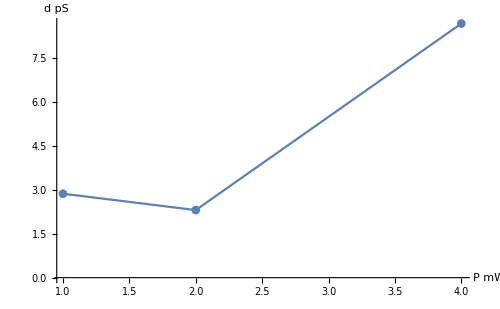

```mathematica
ListLinePlot[
{Sort[Table[{powerDatDict31["longFeb1AB225"][[k]],coef[k][[3,2]]},{k,Keys[coef]}]]},
PlotMarkers->Automatic,
ImageSize->500,
AxesLabel->{"P mW","d pS"},
LabelStyle->{Black,14},
Mesh->Full,
PlotRange->All
]
```